```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 70 Kb

{Utilities`CleanSlate`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
Clear[T]
T =  1/2 M x1'[t]^2+ 1/2 m x2'[t]^2 + 1/2 M x3'[t]^2
```

1/2 M x1'[t]^2+1/2 m x2'[t]^2+1/2 M x3'[t]^2

```mathematica
Clear[V]
V = 1/2 k ( x2[t]-x1[t] )^2 + 1/2 k ( x3[t]-x2[t] )^2
```

1/2 k (-x1[t]+x2[t])^2+1/2 k (-x2[t]+x3[t])^2

```mathematica
Clear[ℒ]
ℒ = T - V
```

-1/2 k (-x1[t]+x2[t])^2-1/2 k (-x2[t]+x3[t])^2+1/2 M x1'[t]^2+1/2 m x2'[t]^2+1/2 M x3'[t]^2

```mathematica
Clear[q]
q = { x1[t] , x2[t] , x3[t] }
```

{x1[t],x2[t],x3[t]}

```mathematica
D[ D[ ℒ , D[q[[1]], t] ], t ] - D[ ℒ , q[[1]] ] 
D[ D[ ℒ , D[q[[2]], t] ], t ] - D[ ℒ , q[[2]] ] 
D[ D[ ℒ , D[q[[3]], t] ], t ] - D[ ℒ , q[[3]] ]
```

-k (-x1[t]+x2[t])+M x1''[t]

k (-x1[t]+x2[t])-k (-x2[t]+x3[t])+m x2''[t]

k (-x2[t]+x3[t])+M x3''[t]

```mathematica
Table[
D[ D[ ℒ , D[q[[i]], t] ], t ] - D[ ℒ , q[[i]] ]== 0  ,
{ i, 1, 3 } ]  // Expand // TableForm
```

k x1[t]-k x2[t]+M x1''[t]==0
-k x1[t]+2 k x2[t]-k x3[t]+m x2''[t]==0
-k x2[t]+k x3[t]+M x3''[t]==0

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

-k x1[t]+k x2[t]-M x1''[t]==0
k x1[t]-2 k x2[t]+k x3[t]-m x2''[t]==0
k x2[t]-k x3[t]-M x3''[t]==0

```mathematica
Clear[parameters]
parameters = { 
k-> 100 , 
m-> 20 , 
M -> 60 
} ;
```

```mathematica
parameters // TableForm
```

k→100
m→20
M→60

```mathematica
eqs /. parameters // TableForm
```

-100 x1[t]+100 x2[t]-60 x1''[t]==0
100 x1[t]-200 x2[t]+100 x3[t]-20 x2''[t]==0
100 x2[t]-100 x3[t]-60 x3''[t]==0

```mathematica
Clear[ics]
ics = { 
x1[0] == 0 ,
x1'[0] == 2 ,
x2[0] == 1 , 
x2'[0] == -2 ,
x3'[0] == 2 ,
x3'[0] == -1.5 
} ;
ics // TableForm
```

x1[0]==0
x1'[0]==2
x2[0]==1
x2'[0]==-2
x3'[0]==2
x3'[0]==-1.5

```mathematica
Clear[solution]
solution[t_] = 
First[ NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0, 10 } ]  ]
```

{x1[t]→InterpolatingFunction[…][t],x2[t]→InterpolatingFunction[…][t],x3[t]→InterpolatingFunction[…][t]}

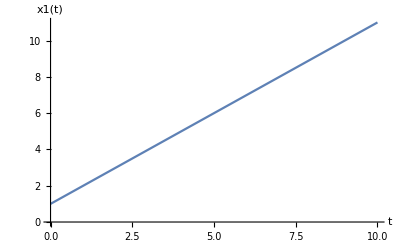

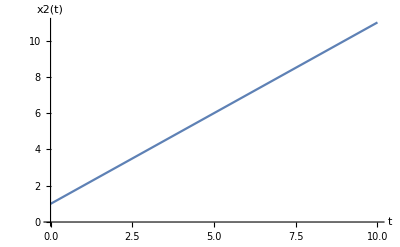

-Graphics-

```mathematica
Plot[ Evaluate[ x1[t] /. solution[t] ]  , { t, 0, 10 }  , AxesLabel-> { t , q[[1]] } ] 
Plot[ Evaluate[ x2[t] /. solution[t] ]  , { t, 0, 10 }  , AxesLabel-> { t , q[[2]] } ] 
Plot[ Evaluate[ x2[t] /. solution[t] ]  , { t, 0, 10 }  , AxesLabel-> { t , q[[2]] } ]
```

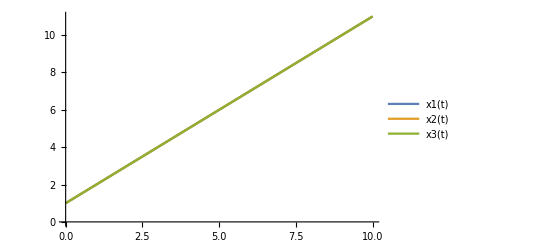

```mathematica
Plot[ Evaluate[ q/. solution [t] ] , { t, 0, 10 }  , PlotLegends-> q ]
```

```mathematica
Clear[trial]
trial = { 
x1[t] -> x[1] Exp[ ⅈ ω t ] ,
x2[t] -> x[2] Exp[ ⅈ ω t ] ,
x3[t] -> x[3] Exp[ ⅈ ω t ] 
} ;
trial // TableForm
```

x1[t]→ⅇ^(ⅈ t ω) x[1]
x2[t]→ⅇ^(ⅈ t ω) x[2]
x3[t]→ⅇ^(ⅈ t ω) x[3]

```mathematica
D[trial, t] // TableForm
```

x1'[t]→ⅈ ⅇ^(ⅈ t ω) ω x[1]
x2'[t]→ⅈ ⅇ^(ⅈ t ω) ω x[2]
x3'[t]→ⅈ ⅇ^(ⅈ t ω) ω x[3]

```mathematica
D[D[trial, t], t] // TableForm
```

x1''[t]→-ⅇ^(ⅈ t ω) ω^2 x[1]
x2''[t]→-ⅇ^(ⅈ t ω) ω^2 x[2]
x3''[t]→-ⅇ^(ⅈ t ω) ω^2 x[3]

```mathematica
eqs //. trial  //. D[D[trial, t], t] // TableForm
```

-ⅇ^(ⅈ t ω) k x[1]+ⅇ^(ⅈ t ω) M ω^2 x[1]+ⅇ^(ⅈ t ω) k x[2]==0
ⅇ^(ⅈ t ω) k x[1]-2 ⅇ^(ⅈ t ω) k x[2]+ⅇ^(ⅈ t ω) m ω^2 x[2]+ⅇ^(ⅈ t ω) k x[3]==0
ⅇ^(ⅈ t ω) k x[2]-ⅇ^(ⅈ t ω) k x[3]+ⅇ^(ⅈ t ω) M ω^2 x[3]==0

```mathematica
eqs //. trial  //. D[D[trial, t], t] // Simplify // TableForm
```

ⅇ^(ⅈ t ω) (M ω^2 x[1]+k (-x[1]+x[2]))==0
ⅇ^(ⅈ t ω) (m ω^2 x[2]+k (x[1]-2 x[2]+x[3]))==0
ⅇ^(ⅈ t ω) (k (x[2]-x[3])+M ω^2 x[3])==0

```mathematica
Clear[secularEq]
secularEq = 
Assuming[ Exp[ ⅈ ω t ] ≠ 0 ,
DivideSides[ eqs //. trial  //. D[D[trial, t], t]   , Exp[ ⅈ ω t ] ] ] // Expand  ; 
secularEq // TableForm
```

-k x[1]+M ω^2 x[1]+k x[2]==0
k x[1]-2 k x[2]+m ω^2 x[2]+k x[3]==0
k x[2]-k x[3]+M ω^2 x[3]==0

```mathematica
Clear[secularDet]
secularDet = 
Table[ 
Coefficient[ secularEq[[i,1]] , { x[1] , x[2] , x[3] } ] ,
{ i , 1, 3 } ]  ; 
secularDet // MatrixForm
```

(-k+M ω^2 | k | 0
k | -2 k+m ω^2 | k
0 | k | -k+M ω^2)

```mathematica
Solve[ Det[ secularDet ] == 0 , ω ] 
Solve[ Det[ secularDet ] == 0 , ω ][[2]]
Solve[ Det[ secularDet ] == 0 , ω ][[4]]
Solve[ Det[ secularDet ] == 0 , ω ][[6]]
```

{{ω→0},{ω→0},{ω→-(√k)/(√M)},{ω→(√k)/(√M)},{ω→-(√k √(m+2 M))/(√m √M)},{ω→(√k √(m+2 M))/(√m √M)}}

{ω→0}

{ω→(√k)/(√M)}

{ω→(√k √(m+2 M))/(√m √M)}

```mathematica
Clear[ω1Replace]
ω1Replace = 
Solve[ Det[ secularDet ] == 0 , ω ][[2]]
```

{ω→0}

```mathematica
Clear[ω2Replace]
ω2Replace = 
Solve[ Det[ secularDet ] == 0 , ω ][[4]]
```

{ω→(√k)/(√M)}

```mathematica
Clear[ω3Replace]
ω3Replace = 
Solve[ Det[ secularDet ] == 0 , ω ][[6]]
```

{ω→(√k √(m+2 M))/(√m √M)}

```mathematica
Clear[ωReplace]
ωReplace = Union[ ω1Replace , ω2Replace, ω3Replace ]
```

{ω→0,ω→(√k)/(√M),ω→(√k √(m+2 M))/(√m √M)}

```mathematica
secularDet  // MatrixForm
```

(-k+M ω^2 | k | 0
k | -2 k+m ω^2 | k
0 | k | -k+M ω^2)

```mathematica
Clear[X]
X = { x[1] , x[2] , x[3] } 
Clear[zero]
zero = { 0 , 0, 0 }
```

{x[1],x[2],x[3]}

{0,0,0}

```mathematica
Solve[
Thread[ ( secularDet /. ω1Replace )  . X == 0 ] , X ]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x[2]→x[1],x[3]→x[1]}}

```mathematica
Solve[
Thread[ ( secularDet /. ω2Replace )  . X == 0 ] , X ]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x[2]→0,x[3]→-x[1]}}

```mathematica
Solve[
Thread[ ( secularDet /. ω3Replace )  . X == 0 ] , X ]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x[2]→-(2 M x[1])/m,x[3]→x[1]}}

```mathematica
Divisors[integer]
```

Divisors[integer]